```mathematica
pressures={8,10,11.6,13,14,14.5,15};
area = {97.667,68.378,53.509,36.448,27.556,24.196,21.551};
c=0.5611415;
data=Transpose[{pressures*c,area}];
```

```mathematica
linearFit = Fit[data[[1;;4]],{1,x},x]
```

192.059-21.4283 x

```mathematica
linearFit2= Fit[data[[4;;7]],{1,x},x]
```

134.096-13.4565 x

```mathematica
2Sqrt[2 13.46/(2 π) Log[2]]//N(*focus diameter in μm*)
```

3.4466

```mathematica
Sqrt[13.46/(2π)]*2.355
```

3.44686

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*Error estimate to be 10% of actual size, as microscope area measuring method is tedious & unprecise. Certainly another correction for small pressures should be done...*)
```

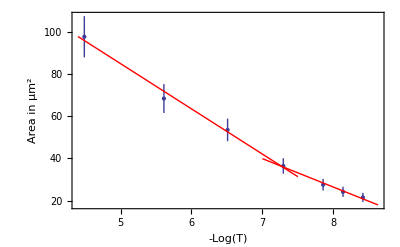

```mathematica
Show[ErrorListPlot[Transpose[{data,Table[ErrorBar[area[[i]]*0.10],{i,1,7}]}],
Frame->True,PlotStyle->Directive[PointSize[Large]],FrameLabel->{"-Log(T)","Area in μm^2"},FrameStyle->Directive[12],Axes->None],Plot[linearFit,{x,4.4,7.5},PlotStyle->Directive[Red,Thick]],Plot[linearFit2,{x,7.0,8.63},PlotStyle->Directive[Red,Thick]]]
```

```mathematica
(*From Henke LBL database. Transmission of N2 over 410cm attenuation length at 1600 eV *)
```

```mathematica
attenuation=Log@{0.11230 10^-1,0.36559 10^-2,0.14896 10^-2,0.67904 10^-3,0.38743 10^-3,0.29265 10^-3,0.22105 10^-3}
```

{-4.48917,-5.61141,-6.50925,-7.29483,-7.85598,-8.13653,-8.41712}

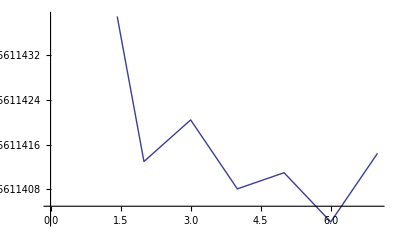

```mathematica
ListLinePlot[-attenuation/pressures]
```